# Report Project 2

Course code: IX1500
Date: 2020-09-24

Simon Johannesson, sijohann@kth.se
William Asp, wasp@kth.se

Task 1: Put title here

## Summary

### Task

#### Task 1

empty

#### Task 2

empty

### Result

#### Task 1

empty

#### Task 2

empty

## Calculations

### Equations

#### Task 1

empty

#### Task 2

empty

### Discussion

Empty

#### Task 1

empty

#### Task 2

empty

### Diagrams

Empty

#### Task 1

empty

#### Task 2

empty

### Conclusion

Empty

#### Task 1

empty

#### Task 2

empty

## Code

### Task 1

Empty

### Task 2

#### Trying to fit a model to our data

The dataset below contains the calculations of the time to crack a cipher of different bit sizes of n. The left value is The bit size, and the right value is the time to crack the cipher.

```mathematica
data={{100,0.051393},{105,0.052793},{110,0.077445},{115,0.07904},{120,0.107998},{125,0.135188},{130,0.264322},{135,0.290357},{140,0.422595},{145,0.464552},{150,0.988578},{155,1.713563},{160,3.72046},{165,4.769045},{170,6.235202},{175,8.115938},{180,13.510855},{185,16.892628},{190,33.129527},{195,34.235115},{200,110.100646}};
```

Let’s split the data so it is easier to work with.
The bit sizes of n:

```mathematica
𝕩=data[[All,1]]
```

{100,105,110,115,120,125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200}

The times to crack the cipher:

```mathematica
𝕪=data[[All,2]]
```

{0.051393,0.052793,0.077445,0.07904,0.107998,0.135188,0.264322,0.290357,0.422595,0.464552,0.988578,1.71356,3.72046,4.76905,6.2352,8.11594,13.5109,16.8926,33.1295,34.2351,110.101}

Let’s plot the data so we see what we’re working with.

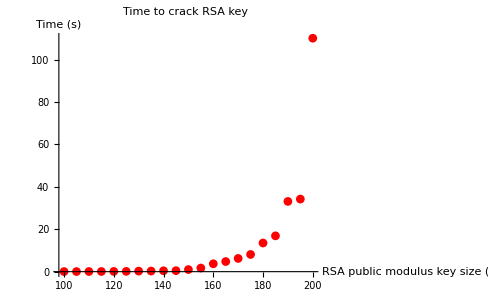

```mathematica
dataplot=ListPlot[data,PlotRange->Full,
PlotStyle->Red,
PlotLabel->"Time to crack RSA key",
AxesLabel->{"RSA public modulus key size (bits)","Time (s)"}]
```

From the dataplot, we believe the data to grow exponentially. If it is exponential the data should give a straight line in a semi-log plot (lin-log plot) in which the x-axis is linear and the y-axis is logarithmic. The scale on the y-axis is chosen using the inverse function y=e^x⇔ln(y)=x.

y=c e^(a x)⇔ln(y)=ln(c)+k x⇔ln(y)=a x+b⇔y=e^(a x+b)

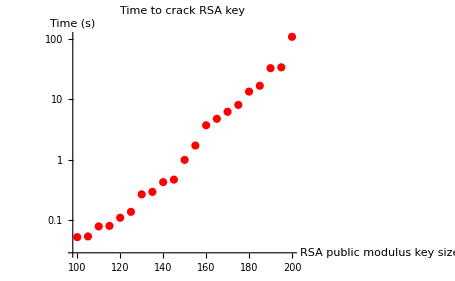

```mathematica
datalogplot=ListLogPlot[data,PlotStyle->Red,
PlotLabel->"Time to crack RSA key",
AxesLabel->{"RSA public modulus key size (bits)","Time (s)"}]
```

Here we see that the data fits pretty good as an exponential function, since the data is in a pretty straight line.

If the data fits a straight line in a log(y)-lin(x) plot, then the model is an exponential function. We want to fit a model to our data, and to do that we need to perform the log operation on the Y values, to be able to fit our model to the data in a straight line.

```mathematica
dataWithLog=Transpose[{𝕩,Log[𝕪]}]
```

{{100,-2.96825},{105,-2.94138},{110,-2.55819},{115,-2.5378},{120,-2.22564},{125,-2.00109},{130,-1.33059},{135,-1.23664},{140,-0.861341},{145,-0.766682},{150,-0.0114877},{155,0.538575},{160,1.31385},{165,1.56215},{170,1.83021},{175,2.09383},{180,2.60349},{185,2.82688},{190,3.50042},{195,3.53325},{200,4.70139}}

Find a fitting model to the data. Find the best values for a and b to make a linear function that fits our dataWithLog.

```mathematica
solution=FindFit[dataWithLog,a x+b,{a,b},x]
```

{a→0.0771778,b→-11.3355}

The linear function should now fit our dataWithLog.
We plug the a and b values into a function that will output a predicted y value based on the x value.

```mathematica
y[x_]=ⅇ^(a x+b)/.solution
```

ⅇ^(-11.3355+0.0771778 x)

Let’s see if the model fits out data.

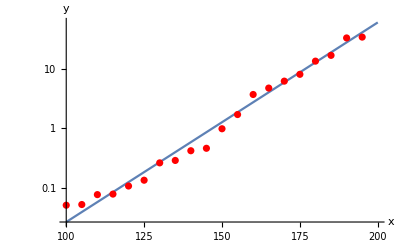

```mathematica
modelplot=LogPlot[y[x],{x,100,200},AxesLabel->{x,y}];
Show[modelplot,dataplot]
```

Yes we think that the model fits our data!
Let’s see how it fits in a normal x and y coordinate system, without the log on the data or coordinate system.

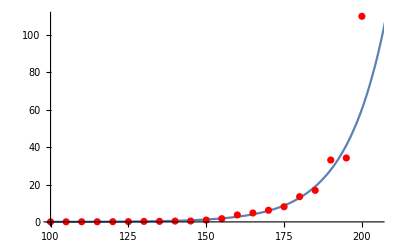

```mathematica
model=Plot[y[x],{x,100,250},PlotRange->All];
Show[model,dataplot,PlotRange->{{100,205},{0,110}}]
```

We think that the result looks good! We can now find out approximately how long it will take to crack a cipher that is longer.

#### Finding out approximately how much time it will take to crack a cipher where n is 1024, 2048 or 4096 bits long.

Cracking a cipher of 1024 bits:

```mathematica
y[1024]
```

2.50825×10^29

The result we get here is in seconds, lets find out how many years that is!

```mathematica
secondsToYears[seconds_]:=seconds/60/60/24/365
```

```mathematica
secondsToYears[y[1024]]
```

7.95362×10^21

That is a lot of years.
Let’s see for bigger numbers.

```mathematica
secondsToYears[y[2048]]
```

1.67059×10^56

```mathematica
secondsToYears[y[4096]]
```

7.37027×10^124